```mathematica
Clear["Global`*"];
Off[General::spell];
Off[General::spell1];
```

### 4a

```mathematica
x[n_, m_] := Sqrt[(n+m+1)]/2 /; Abs[n-m] == 1
x[n_, m_] := 0 /; Abs[n-m] != 1
```

```mathematica
p[n_, m_] := I Sqrt[(n+m+1)]/2 /; n - m == 1
p[n_, m_] := -I Sqrt[(n+m+1)]/2 /; n - m == -1
p[n_, m_] := 0 /; Abs[n-m] != 1
```

```mathematica
x[basissize_] := Table[
x[n, m], 
{n, 0, basissize-1}, 
{m, 0, basissize-1} 
]
```

```mathematica
p[basissize_] := Table[
p[n,  m],  
{n, 0, basissize - 1}, 
{m, 0, basissize - 1} 
]
```

```mathematica
h0[basissize_] := DiagonalMatrix [ 
Table[n+1/2, 
{n, 0, basissize-1} 
]
 ]
```

```mathematica
h[basissize_, λ_] := h0[basissize] -x[basissize].x[basissize]+λ x[basissize].x[basissize].x[basissize].x[basissize]/4
```

```mathematica
evals[basissize_, λ_] := Sort [ Eigenvalues [ N[ h[basissize,  λ] ] ] ]
```

```mathematica
e=evals[50,0.2]
```

{-0.632746,-0.57653,0.254744,0.771773,1.55257,2.41806,3.37842,4.41736,5.52667,6.69968,7.93112,9.21671,10.5528,11.9364,13.3648,14.8357,16.347,17.897,19.484,21.1065,22.7631,24.4528,26.1746,27.9277,29.7077,31.5113,33.3595,35.2774,37.0886,38.763,40.9275,43.7495,44.3312,46.5255,53.4078,53.4867,66.5115,66.5435,83.9692,83.9896,106.865,106.88,136.928,136.94,176.998,177.008,232.369,232.377,316.152,316.159}

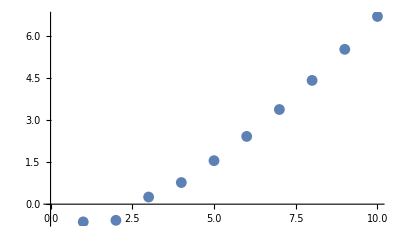

```mathematica
ListPlot[Part[e,1;;10]]
```

Two negative eigenstates.

### 4b

```mathematica
e=evals[50,0.05]
```

{-4.30594,-4.30594,-2.97487,-2.97485,-1.74578,-1.7445,-0.676914,-0.637768,0.0861448,0.39026,0.9469,1.50551,2.12624,2.78593,3.48304,4.21389,4.9761,5.76766,6.58693,7.43248,8.30309,9.19766,10.1153,11.0548,12.016,12.4021,12.9977,13.9993,15.023,16.0594,17.1302,18.1949,19.2952,20.4021,21.574,22.6088,24.0839,25.0508,26.4267,27.4036,29.2204,29.3975,33.3087,33.6753,35.5407,35.8685,40.3258,41.6211,49.5144,49.9108}

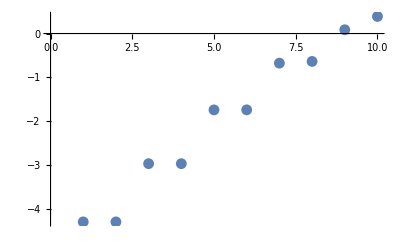

```mathematica
ListPlot[Part[Sort[e],1;;10]]
```

Four negative pairs of energies.

Plot the predicted result

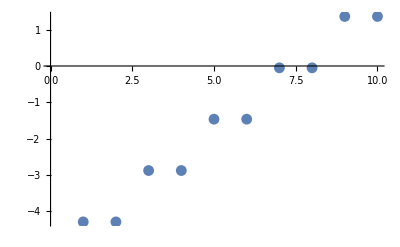

```mathematica
ListPlot[Table[-1/(4*.05)+(Floor[n/2] + 1/2)*Sqrt[2],{n,0,9}]]
```

Plot the error

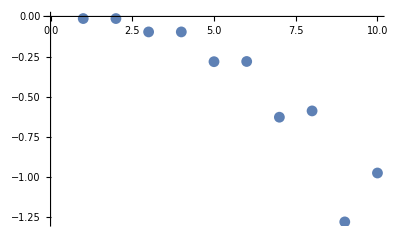

```mathematica
ListPlot[Table[e[[n+1]]-(-1/(4*.05)+(Floor[(n)/2] + 1/2)*Sqrt[2]),{n,0,9}]]
```

The level splitting can still be seen even though the approximation begines to degrade